```mathematica
f1:=1-μ/(3 r^2)
```

```mathematica
f2:=1+r^2/(4 α)-(√(3 r^4+48 α^2+8 α μ))/(4 √3 α)
```

```mathematica
funcion:=(r^4+α^2-(r^4+2 r^2 α+3 α^2) f[r]+α (r^2+3 α) f[r]^2-α^2 f[r]^3)/r^2
f3:=f[r]/. Solve[funcion1==μ,f[r],Reals][[1]]
```

```mathematica
α:=0.03
μ:=1
```

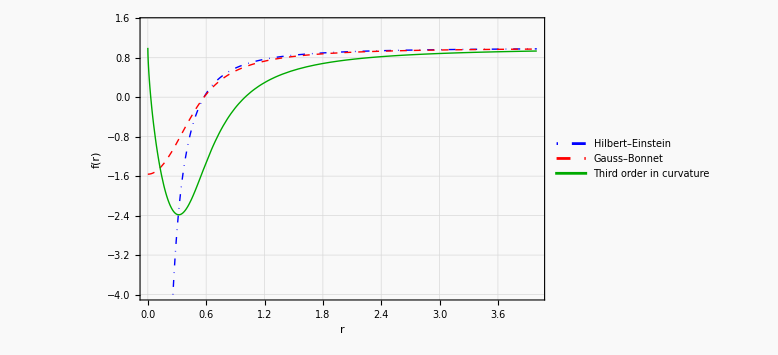

```mathematica
graphf3=Plot[{f1,f2,f3},{r,0,4},PlotStyle->{{Thick,DotDashed,Blue},{Thick,Dashed,Red},{Thick,Darker[Green]}},AxesLabel->{"r","f(r)"},LabelStyle->{FontSize->14,Bold,Black},PlotLegends->Placed[{"Hilbert–Einstein","Gauss–Bonnet","Third order in curvature"},{0.75,0.35}],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed,Opacity[0.5]],Background->Lighter[Gray,0.95],Frame->True,FrameLabel->{"r","f(r)",None,None},FrameStyle->Directive[Black,14],ImageSize->Large,PlotRange->{-4,1.5}]
```

```mathematica
Export["Comparando agujeros negros.png",graphf3]
```

Comparando agujeros negros.png